```mathematica
kx=1;
ky=0;
g=10;
U1 = 15000;
c=20000;
hplus[g_,c2_,kx_,U2_,γ_]:=g/(2 c2^2)+1/2 √(4 kx^2+(g^2+4 c2^2 (γ+I*kx*U2)^2)/c2^4);
hminus[g_,c1_,kx_,U1_,γ_]:=g/(2 c1^2)-1/2 √(4 kx^2+(g^2+4 c1^2 (γ+I*kx*U1)^2)/c1^4);
gamma[g_,c_,kx_,U1_,U2_]:=  ⅈ  c kx (-(U1+U2)/(2 c)+ √((- ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√((1-(ⅈ  g)/(2 c^2 kx))^2+((U1-U2)/c)^2)));
gammatest[g_,c_,kx_,U1_,U2_]:=1/2 ⅈ (-kx (U1+U2)+ 2 c kx √((- ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√(-g^2/(4 c^4 kx^2)-(ⅈ  g)/(c^2 kx)+1+((U1-U2)/c)^2)));
gamma2[g_,c_,kx_,U1_,U2_]:=  ⅈ  c kx (-(U1+U2)/(2 c)+ √((ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√((1+(ⅈ  g)/(2 c^2 kx))^2+((U1-U2)/(2c))^2)));
hplusnog[c2_,kx_,U2_,γ_]:=√(kx^2+ (γ+I*kx*U2)^2/c2^2)
hminusnog[c1_,kx_,U1_,γ_]:=-√(kx^2+ (γ+I*kx*U1)^2/c1^2)
gammanog[c_,kx_,U1_,U2_]:=1/-2*I*kx*(U1+U2)-I*kx*c*√((U1-U2)^2/(4 c^2)+1-√(1+(U1-U2)^2/c^2));
```

Normalized versions

```mathematica
hplusnorm[L_,M2_,γ_]:=1/(2 L)+ √(1+1/(4 L^2)+(γ+I*M2)^2);
hminusnorm[L_,M1_,γ_]:=1/(2 L)-√(1+1/(4 L^2)+(γ+I*M1)^2);
gammanorm[L_,M1_,Mc_]:=  ⅈ   (-(M1+Mc)+√((- ⅈ)/(2 L)+1+(Mc)^2-√((1-ⅈ/(2 L))^2+4 Mc^2)));
gamma2[g_,c_,kx_,U1_,U2_]:=  ⅈ  c kx (-(U1+U2)/(2 c)+ √((ⅈ g)/(2 c^2 kx)+1+(U1- U2)^2/(4 c^2)-√((1+(ⅈ  g)/(2 c^2 kx))^2+((U1-U2)/(2c))^2)));
hplusnognorm[M2_,γ_]:=√(1+ (γ+I*M2)^2)
hminusnognorm[M1_,γ_]:=-√(1+ (γ+I*M1)^2)
gammanognorm[M1_,Mc_]:=I(-(M1+Mc)-√(Mc^2+1-√(1+4 Mc^2)));
```

First let us look at the normalized growth rates.

```mathematica
Manipulate[Plot[{Re[gammanorm[L,M1,Mc]],Re[gammanognorm[M1,Mc]]},{Mc,0,5},ImageSize->800,PlotLegends->Automatic,PlotRange->All],{L,1,0.01}]
```

No noticeable difference so let us look at the difference

```mathematica
Manipulate[LogPlot[{Abs[Re[gammanorm[L,M1,Mc]]-Re[gammanognorm[M1,Mc]]]},{Mc,0,2},ImageSize->800],{L,1000,1}]
```

As we can see, unless L is very small the differences are not noticeable.
Now let us look at the h values

Plot of hminus with and without g, in this case L

```mathematica
M1=1;
Manipulate[Plot[{Re[N[hminusnorm[L,M1,gammanorm[L,M1,Mc]]]],Re[N[hminusnognorm[M1,gammanognorm[M1,Mc]]]]},{Mc,0,2},PlotLegends->Automatic,ImageSize->800],{L,1000,1}]
```

Plot  of  the  difference between the two

```mathematica
Manipulate[LogPlot[{Abs[Re[N[hminusnorm[L,M1,gammanorm[L,M1,Mc]]]]-Re[N[hminusnognorm[M1,gammanognorm[M1,Mc]]]]]},{Mc,0,2},ImageSize->800],{L,1000,1}]
```

Now the same for hplus. First the two plots

```mathematica
M1=1;
Manipulate[Plot[{Re[N[hplusnorm[L,M1+2*Mc,gammanorm[L,M1,Mc]]]],Re[N[hplusnognorm[M1+2*Mc,gammanognorm[M1,Mc]]]]},{Mc,0,2},PlotLegends->Automatic,ImageSize->800],{L,1000,1}]
```

Now the two differences

```mathematica
Manipulate[LogPlot[Abs[Re[N[hplusnorm[L,M1+2*Mc,gammanorm[L,M1,Mc]]]]-Re[N[hplusnognorm[M1+2*Mc,gammanognorm[M1,Mc]]]]],{Mc,0,2},PlotLegends->Automatic,ImageSize->800],{L,1000,1}]
```

We can also look at what the exponentials look like. First lets look at positive z, only the real part. (Excluding the real oscillatory part)

```mathematica
Manipulate[LogPlot[{Re[Exp[z*Re[N[hminusnorm[L,M1,gammanorm[L,M1,Mc]]]]]],Re[Exp[z*Re[N[hminusnognorm[M1,gammanognorm[M1,Mc]]]]]]},{z,0,20},PlotLegends->Automatic,ImageSize->800],{Mc,0,2},{L,1000,1}]
```

```mathematica
Manipulate[Plot[{Re[Exp[z*Re[N[hminusnorm[L,M1,gammanorm[L,M1,2]]]]]]},{z,0,100},PlotLegends->Automatic,ImageSize->800],{L,10,1}]
```

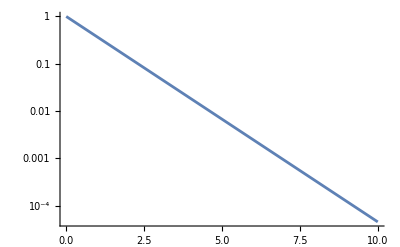

```mathematica
LogPlot[Exp[-1*z],{z,0,10}]
```

We can look at the differences,

```mathematica
Manipulate[LogPlot[Abs[Re[Exp[z*Re[N[hminusnorm[L,M1,gammanorm[L,M1,Mc]]]]]]-Re[Exp[z*Re[N[hminusnognorm[M1,gammanognorm[M1,Mc]]]]]]],{z,0,20},PlotLegends->Automatic,ImageSize->800],{Mc,0,2},{L,1000,1}]
```

Now lets look at the exponential for negative z,

```mathematica
Manipulate[LogPlot[{Re[Exp[-z*Re[N[hplusnorm[L,M1+2Mc,gammanorm[L,M1,Mc]]]]]],Re[Exp[-z*Re[N[hplusnognorm[M1+2Mc,gammanognorm[M1,Mc]]]]]]},{z,0,20},PlotLegends->Automatic,ImageSize->800],{Mc,0,2},{L,1000,1}]
```

And their differences

```mathematica
Manipulate[LogPlot[Abs[Re[Exp[-z*Re[N[hplusnorm[L,M1+2Mc,gammanorm[L,M1,Mc]]]]]]-Re[Exp[-z*Re[N[hplusnognorm[M1+2Mc,gammanognorm[M1,Mc]]]]]]],{z,0,20},PlotLegends->Automatic,ImageSize->800],{Mc,0,2},{L,1000,1}]
```